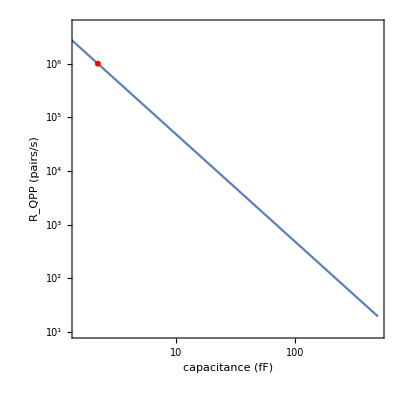

```mathematica
(* Panel D of Figure 3 of the main text *)
(* Plot dependence of decoherence rate on capacitance *)

(* based on results of Panel C, we see how the results scale with capacitance using a value of R_{QPP} of 1 MHz at a capacitance of about 2.2 fF.

excitation rate scales as 1/C^2 *)

(* excitation rate at 2.2 fF is about 1 MHz *)

ClearAll["Global`*"];



(* fix coefficient so that rate at 2.2 fF is 10^6 *)

p1=LogLogPlot[(10^6*(2.2)^2)/(capacitance^2),{capacitance, 1.,500},

Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"capacitance (fF)","R_QPP (pairs/s)",None,None},
PlotRange->{{1.5,500},{10,5*10^6}},
FrameTicks->{{{{1,"1"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"}},None},{{10,100},None}},
AspectRatio->1.,
(* ImageSize->{width,height}:Specifies absolute dimensions in points (e.g.,ImageSize->{500,300}). *)
ImageSize->{Automatic,200}(*:Fixes only the height while letting the width adjust automatically based on the content.*)
];

p2=ListLogLogPlot[{{2.2,10^6}},PlotStyle->Red,PlotMarkers->{●,6}];

Show[p1,p2]
```